```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 2*)
```

```mathematica
u[x_]:=1+Cos[2π x]/(1+x^2)
```

```mathematica
FullSimplify[u''[x]]
```

(-2 (1-3 x^2+2 π^2 (1+x^2)^2) Cos[2 π x]+8 π x (1+x^2) Sin[2 π x])/((1+x^2)^3)

```mathematica
ResourceFunction["HessianMatrix"][u[x,y],{x,y}]//Simplify
```

{{u^(2,0)[x,y],u^(1,1)[x,y]},{u^(1,1)[x,y],u^(0,2)[x,y]}}

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]],t[[i,2]]]],{i,1,Length[t]}]]
```

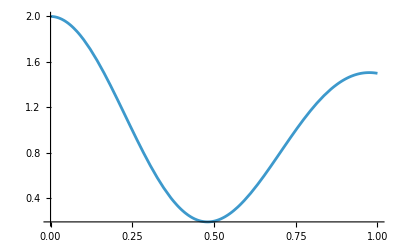

```mathematica
plotexact=Plot[u[x],{x,xl,xr},PlotRange->Full]
```

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}];
```

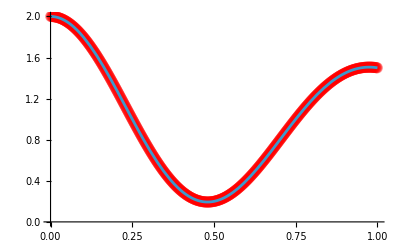

```mathematica
Show[plotnum,plotexact]
```